```mathematica
SetDirectory[NotebookDirectory[]];
```

# Floquet analysis for the island-mainland model

## Floquet Multiplier 1

### Stability plot

```mathematica
lam1data=Import["stability_lam1_data.csv"];
```

```mathematica
legend=BarLegend[
{{ColorData["GrayTones"][Rescale[0.2,{0.2,1}]],
ColorData["GrayTones"][Rescale[0.3,{0.2,1}]],
ColorData["GrayTones"][Rescale[0.4,{0.2,1}]],
ColorData["GrayTones"][Rescale[0.5,{0.2,1}]],
ColorData["GrayTones"][Rescale[0.6,{0.2,1}]],
ColorData["GrayTones"][Rescale[0.7,{0.2,1}]],
ColorData["GrayTones"][Rescale[0.8,{0.2,1}]],
ColorData["GrayTones"][Rescale[0.9,{0.2,1}]],
ColorData["BlueGreenYellow"][Rescale[1.2,{1,1.5}]],
ColorData["BlueGreenYellow"][Rescale[1.45,{1,1.5}]]},
{-1.6,0.4}},{-1.6,-1.4,-1.2,-1.0,-0.8,-0.6,-0.4,-0.2,0.0,0.2,0.4},
LegendLabel->Style[" ",15],
"Ticks"->{-1.4,-1.2,-1,-0.8,-0.6,-0.4,-0.2,0,0.2},
LegendFunction->Frame
]
```

```mathematica
fig=Show[ListContourPlot[lam1data,
RegionFunction->Function[{x,y,z},1-Exp[-2π(BA-y)]>x],
Frame->{{True,True},{True,True}},
FrameStyle->Directive[Black],
FrameLabel->{Style["",15],Style["",15]},
PlotRange->{{0,1},{0,0.2}},
ColorFunction->ColorData["GrayTones"]],
ListContourPlot[lam1data,PlotLegends->Placed[legend,{After,Right}],
RegionFunction->Function[{x,y,z},z>0],InterpolationOrder->100,
Contours->Range[0,1.5,0.2],
Frame->{{True,True},{True,True}},
FrameStyle->Directive[Black],
FrameLabel->{Style["",15],Style["",15]},
ColorFunction->ColorData["BlueGreenYellow"]],
Plot[BA+1/(2π)Log[1-x],{x,0,0.9},PlotStyle->Directive[Black,Thick]],
Plot[Ba+1/(2π)Log[1-x],{x,-0.3,0.9},PlotStyle->Directive[Black,Thick,Dashed],PlotLegends->Placed[LineLegend[{Directive[Black,Thick],Directive[Black,Thick,Dashed],Directive[Blue,Thick]},{" extinction"," extinction","coexistence 
criterion"},
LegendMarkerSize->15, LegendFunction->Frame],{Right,Top}]],
Plot[1/(2π)Log[1-x]+(BA Ba (10000-5000))/(BA 10000 - Ba 5000),{x,-0.3,0.9},PlotStyle->Directive[Blue,Thick]]]
```

-Graphics-

```mathematica
Export["stability_lam1_plot.pdf",fig,"PDF"];
```

# Measuring local adaptation

## Get region of stability

```mathematica
data = Import["stability_lam1_data.csv"];
```

```mathematica
temp=ListContourPlot[data,InterpolationOrder->2,
Contours->{0},
ContourShading->None,
ContourStyle->Directive[Thick,Red],
Frame->{{True,True},{True,True}},
FrameTicks->{{True,False},{True,False}},
FrameLabel->{Style["",15],Style["",15]},
FrameStyle->Directive[Black]];
```

```mathematica
line1=First@Cases[Normal[temp],_Line,Infinity];
line2=Last@Cases[Normal[temp],_Line,Infinity];
```

```mathematica
tval1=ResourceFunction["LeeInterpolatingNodes"][line1[[1]]];
tval2=ResourceFunction["LeeInterpolatingNodes"][line2[[1]]];
```

```mathematica
cc1=Interpolation[Transpose[{tval1,line1[[1]]}],Method->"Spline"];
cc2=Interpolation[Transpose[{tval2,line2[[1]]}],Method->"Spline"];
```

```mathematica
lin1=Table[cc1[s],{s,0,1.03,0.01}];
lin2=Table[cc2[s],{s,0,1.03,0.01}];
```

```mathematica
mr=MeshRegion[DiscretizeRegion[Region[Polygon[Join[lin2,lin1]]]]];
```

## Deterministic

```mathematica
LFinit=Import["local_adaptation_init.csv"];
```

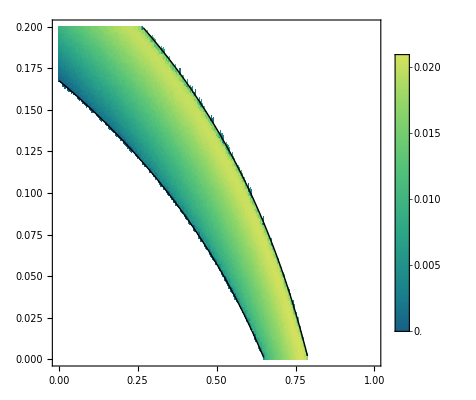

```mathematica
lf0fig=Show[ListDensityPlot[LFinit,PlotRange->{{0,1},{0,0.2},{-0.01,0.022}},
RegionFunction->Function[{x,y,z},z≠0],
InterpolationOrder->0,
PlotLegends->Automatic,
ColorFunction->Function[{z},ColorData["BlueGreenYellow"][Rescale[z,{-0.007,0.022}]]],
Frame->{{True,True},{True,True}},
FrameTicks->{{True,True},{True,True}},
FrameStyle->Directive[Black],
FrameLabel->{Style["",15],Style["",15]},
ColorFunctionScaling->False],ParametricPlot[{cc1[t],cc2[t]},{t,0.003,0.997},PlotStyle->Directive[Black,Thick]]]
```

```mathematica
Export["det_la0_plot.png",lf0fig,"PNG"];
```

```mathematica
LFfinal=Import["local_adaptation_final.csv"];
```

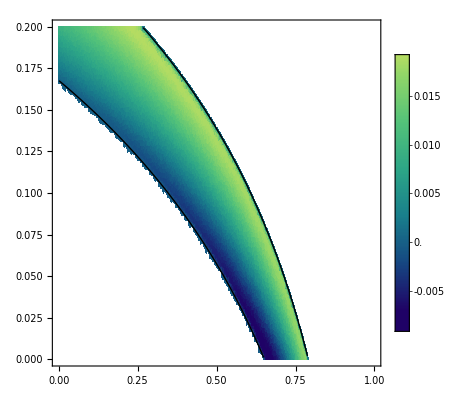

```mathematica
lfffig=Show[ListDensityPlot[LFfinal,PlotRange->{{0,1},{0,0.2},{-0.01,0.022}},
RegionFunction->Function[{x,y,z},z≠0],InterpolationOrder->1,
PlotLegends->Automatic,
ColorFunction->Function[{z},ColorData["BlueGreenYellow"][Rescale[z,{-0.007,0.022}]]],
Frame->{{True,True},{True,True}},
FrameTicks->{{True,True},{True,True}},
FrameStyle->Directive[Black],
FrameLabel->{Style["",15],Style["",15]},
ColorFunctionScaling->False],ParametricPlot[{cc1[t],cc2[t]},{t,0.003,0.997},PlotStyle->Directive[Black,Thick]]]
```

```mathematica
Export["det_laf_plot.png",lfffig,"PNG"];
```

```mathematica
legend=BarLegend[{"BlueGreenYellow",{-0.007,0.022}},

LegendLabel->Style[" ",15],LegendFunction->Frame]
```

## Measuring strength of genetic drift

```mathematica
nesdata=Import["nes_data.csv"];
```

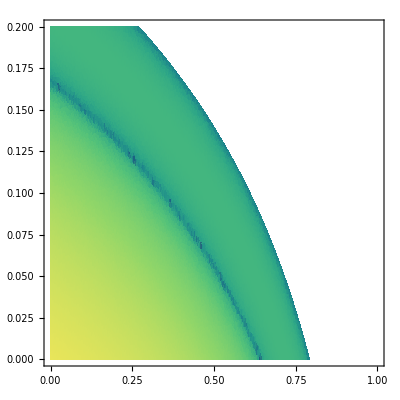

```mathematica
nesfig=ListDensityPlot[nesdata,InterpolationOrder->1,ScalingFunctions->"Log",PlotRange->{{0,1},{0,0.2},All},PlotLegends->BarLegend[Automatic,LegendLabel->Style[" ",15],LegendFunction->Frame],ColorFunction->ColorData["BlueGreenYellow"],Frame->{{True,True},{True,True}},FrameTicks->{{True,True},{True,True}},
FrameStyle->Directive[Black],
FrameLabel->{Style["",15],Style["",15]},
ColorFunctionScaling->True]
```

```mathematica
Export["nes_plot.png",nesfig,"PNG"];
```

## Stochastic

```mathematica
stoLFinit=Import["stoch_local_adaptation_init.csv"];
```

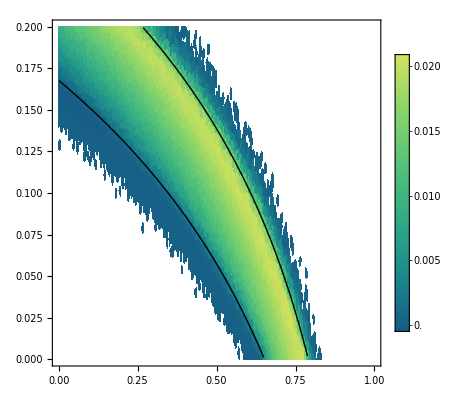

```mathematica
stochla0fig=Show[ListDensityPlot[stoLFinit,PlotRange->All,
RegionFunction->Function[{x,y,z},z≠0],
InterpolationOrder->0,
PlotLegends->Automatic,
ColorFunction->Function[{z},ColorData["BlueGreenYellow"][Rescale[z,{-0.007,0.022}]]],
Frame->{{True,True},{True,True}},
FrameTicks->{{True,True},{True,True}},
FrameStyle->Directive[Black],
FrameLabel->{Style["",15],Style["",15]},
ColorFunctionScaling->False],ParametricPlot[{cc1[t],cc2[t]},{t,0.003,0.997},PlotStyle->Directive[Black,Thick]]]
```

```mathematica
Export["stoch_la0_plot.png",stochla0fig,"PNG"];
```

```mathematica
stoLFfinal=Import["stoch_local_adaptation_final.csv"];
```

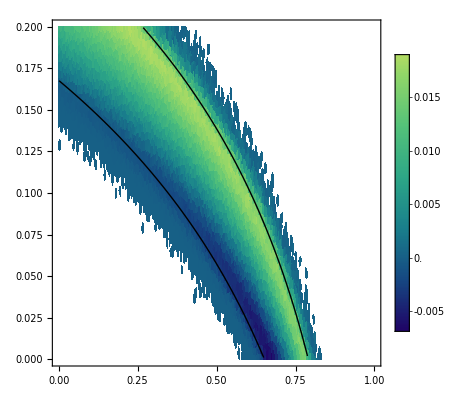

```mathematica
stochlaffig=Show[ListDensityPlot[stoLFfinal,PlotRange->All,
RegionFunction->Function[{x,y,z},z≠0],
InterpolationOrder->0,
PlotLegends->Automatic,
ColorFunction->Function[{z},ColorData["BlueGreenYellow"][Rescale[z,{-0.007,0.022}]]],
Frame->{{True,True},{True,True}},
FrameTicks->{{True,True},{True,True}},
FrameStyle->Directive[Black],
FrameLabel->{Style["",15],Style["",15]},
ColorFunctionScaling->False],ParametricPlot[{cc1[t],cc2[t]},{t,0.003,0.997},PlotStyle->Directive[Black,Thick]]]
```

```mathematica
Export["stoch_laf_plot.png",stochlaffig,"PNG"];
```